## Dimensionful flow equation

```mathematica
dtV=k^4/(4 π^2)((Nf^2-1)2/3 1/(√(1+mpibar2))(1/2+1/(Exp[(k √(1+mpibar2))/T]-1))+2/3 1/(√(1+msigmabar2))(1/2+1/(Exp[(k √(1+msigmabar2))/T]-1))-4Nc Nf 2/3 1/(2 √(1+mfbar2))(1-1/(Exp[(k √(1+mfbar2)-mu)/T]+1)-1/(Exp[(k √(1+mfbar2)+mu)/T]+1)))
```

## Dimensionless flow equation

```mathematica
dtVbar[rho_]:=-3Vbar[rho]+rho lam1bar[rho]+1/(4 π^2 Ttilde)((Nf^2-1)2/3 1/(√(1+lam1bar[rho]))(1/2+1/(Exp[(√(1+lam1bar[rho]))/Ttilde]-1))+2/3 1/(√(1+(lam1bar[rho]+2rho lam2bar[rho])))(1/2+1/(Exp[(√(1+(lam1bar[rho]+2rho lam2bar[rho])))/Ttilde]-1))-4Nc Nf 2/3 1/(2 √(1+(h^2 rho)/2 Ttilde))(1-1/(Exp[(√(1+(h^2 rho)/2 Ttilde)-mutilde)/Ttilde]+1)-1/(Exp[(√(1+(h^2 rho)/2 Ttilde)+mutilde)/Ttilde]+1)));
dtlam1[rho_]:=D[dtVbar[rho],rho]
dtlam2[rho_]:=D[dtlam1[rho],rho]
dtlam3[rho_]:=D[dtlam2[rho],rho]
rep={lam1bar[rho]->lam1bar,lam2bar[rho]->lam2bar,lam1bar'[rho]->lam2bar,lam2bar'[rho]->lam3bar,Vbar'[rho]->lam1bar,lam1bar''[rho]->lam3bar,lam2bar''[rho]->0,Vbar''[rho]->lam2bar,Derivative[3][lam1bar][rho]->0,Derivative[3][lam2bar][rho]->0,Derivative[3][Vbar][rho]->lam3bar};
dtlam1exp=dtlam1[rho]/.rep/.{rho->0,Nc->3,Nf->2};
dtlam2exp=dtlam2[rho]/.rep/.{rho->0,Nc->3,Nf->2};
dtlam3exp=dtlam3[rho]/.rep/.{rho->0,Nc->3,Nf->2};
dtlam1fun[h_,Ttilde_,mutilde_,lam1bar_,lam2bar_,lam3bar_]:=-2 lam1bar+(-8 ((ⅇ^((1-mutilde)/Ttilde) h^2)/(4 (1+ⅇ^((1-mutilde)/Ttilde))^2)+(ⅇ^((1+mutilde)/Ttilde) h^2)/(4 (1+ⅇ^((1+mutilde)/Ttilde))^2))-(2 (1/2+1/(-1+ⅇ^((√(1+lam1bar))/Ttilde))) lam2bar)/(1+lam1bar)^(3/2)-(2 ⅇ^((√(1+lam1bar))/Ttilde) lam2bar)/((-1+ⅇ^((√(1+lam1bar))/Ttilde))^2 (1+lam1bar) Ttilde)+2 (1-1/(1+ⅇ^((1-mutilde)/Ttilde))-1/(1+ⅇ^((1+mutilde)/Ttilde))) h^2 Ttilde)/(4 π^2 Ttilde)
dtlam2fun[h_,Ttilde_,mutilde_,lam1bar_,lam2bar_,lam3bar_]:=-lam2bar+1/(4 π^2 Ttilde)((6 (1/2+1/(-1+ⅇ^((√(1+lam1bar))/Ttilde))) lam2bar^2)/(1+lam1bar)^(5/2)-(8 (1/2+1/(-1+ⅇ^((√(1+lam1bar))/Ttilde))) lam3bar)/(3 (1+lam1bar)^(3/2))+(4 ⅇ^((2 √(1+lam1bar))/Ttilde) lam2bar^2)/((-1+ⅇ^((√(1+lam1bar))/Ttilde))^3 (1+lam1bar)^(3/2) Ttilde^2)-(2 ⅇ^((√(1+lam1bar))/Ttilde) lam2bar^2)/((-1+ⅇ^((√(1+lam1bar))/Ttilde))^2 (1+lam1bar)^(3/2) Ttilde^2)+(6 ⅇ^((√(1+lam1bar))/Ttilde) lam2bar^2)/((-1+ⅇ^((√(1+lam1bar))/Ttilde))^2 (1+lam1bar)^2 Ttilde)-(8 ⅇ^((√(1+lam1bar))/Ttilde) lam3bar)/(3 (-1+ⅇ^((√(1+lam1bar))/Ttilde))^2 (1+lam1bar) Ttilde)+4 h^2 ((ⅇ^((1-mutilde)/Ttilde) h^2)/(4 (1+ⅇ^((1-mutilde)/Ttilde))^2)+(ⅇ^((1+mutilde)/Ttilde) h^2)/(4 (1+ⅇ^((1+mutilde)/Ttilde))^2)) Ttilde-3/2 (1-1/(1+ⅇ^((1-mutilde)/Ttilde))-1/(1+ⅇ^((1+mutilde)/Ttilde))) h^4 Ttilde^2-8 (-(ⅇ^((2 (1-mutilde))/Ttilde) h^4)/(8 (1+ⅇ^((1-mutilde)/Ttilde))^3)+(ⅇ^((1-mutilde)/Ttilde) h^4)/(16 (1+ⅇ^((1-mutilde)/Ttilde))^2)-(ⅇ^((2 (1+mutilde))/Ttilde) h^4)/(8 (1+ⅇ^((1+mutilde)/Ttilde))^3)+(ⅇ^((1+mutilde)/Ttilde) h^4)/(16 (1+ⅇ^((1+mutilde)/Ttilde))^2)-(ⅇ^((1-mutilde)/Ttilde) h^4 Ttilde)/(16 (1+ⅇ^((1-mutilde)/Ttilde))^2)-(ⅇ^((1+mutilde)/Ttilde) h^4 Ttilde)/(16 (1+ⅇ^((1+mutilde)/Ttilde))^2)));
dtlam3fun[h_,Ttilde_,mutilde_,lam1bar_,lam2bar_,lam3bar_]:=1/(4 π^2 Ttilde)(-(75 (1/2+1/(-1+ⅇ^((√(1+lam1bar))/Ttilde))) lam2bar^3)/(2 (1+lam1bar)^(7/2))+(27 (1/2+1/(-1+ⅇ^((√(1+lam1bar))/Ttilde))) lam2bar lam3bar)/(1+lam1bar)^(5/2)-(15 ⅇ^((3 √(1+lam1bar))/Ttilde) lam2bar^3)/((-1+ⅇ^((√(1+lam1bar))/Ttilde))^4 (1+lam1bar)^2 Ttilde^3)+(15 ⅇ^((2 √(1+lam1bar))/Ttilde) lam2bar^3)/((-1+ⅇ^((√(1+lam1bar))/Ttilde))^3 (1+lam1bar)^2 Ttilde^3)-(5 ⅇ^((√(1+lam1bar))/Ttilde) lam2bar^3)/(2 (-1+ⅇ^((√(1+lam1bar))/Ttilde))^2 (1+lam1bar)^2 Ttilde^3)-(30 ⅇ^((2 √(1+lam1bar))/Ttilde) lam2bar^3)/((-1+ⅇ^((√(1+lam1bar))/Ttilde))^3 (1+lam1bar)^(5/2) Ttilde^2)+(15 ⅇ^((√(1+lam1bar))/Ttilde) lam2bar^3)/((-1+ⅇ^((√(1+lam1bar))/Ttilde))^2 (1+lam1bar)^(5/2) Ttilde^2)+(18 ⅇ^((2 √(1+lam1bar))/Ttilde) lam2bar lam3bar)/((-1+ⅇ^((√(1+lam1bar))/Ttilde))^3 (1+lam1bar)^(3/2) Ttilde^2)-(9 ⅇ^((√(1+lam1bar))/Ttilde) lam2bar lam3bar)/((-1+ⅇ^((√(1+lam1bar))/Ttilde))^2 (1+lam1bar)^(3/2) Ttilde^2)-(75 ⅇ^((√(1+lam1bar))/Ttilde) lam2bar^3)/(2 (-1+ⅇ^((√(1+lam1bar))/Ttilde))^2 (1+lam1bar)^3 Ttilde)+(27 ⅇ^((√(1+lam1bar))/Ttilde) lam2bar lam3bar)/((-1+ⅇ^((√(1+lam1bar))/Ttilde))^2 (1+lam1bar)^2 Ttilde)-9/2 h^4 ((ⅇ^((1-mutilde)/Ttilde) h^2)/(4 (1+ⅇ^((1-mutilde)/Ttilde))^2)+(ⅇ^((1+mutilde)/Ttilde) h^2)/(4 (1+ⅇ^((1+mutilde)/Ttilde))^2)) Ttilde^2+15/8 (1-1/(1+ⅇ^((1-mutilde)/Ttilde))-1/(1+ⅇ^((1+mutilde)/Ttilde))) h^6 Ttilde^3+6 h^2 Ttilde (-(ⅇ^((2 (1-mutilde))/Ttilde) h^4)/(8 (1+ⅇ^((1-mutilde)/Ttilde))^3)+(ⅇ^((1-mutilde)/Ttilde) h^4)/(16 (1+ⅇ^((1-mutilde)/Ttilde))^2)-(ⅇ^((2 (1+mutilde))/Ttilde) h^4)/(8 (1+ⅇ^((1+mutilde)/Ttilde))^3)+(ⅇ^((1+mutilde)/Ttilde) h^4)/(16 (1+ⅇ^((1+mutilde)/Ttilde))^2)-(ⅇ^((1-mutilde)/Ttilde) h^4 Ttilde)/(16 (1+ⅇ^((1-mutilde)/Ttilde))^2)-(ⅇ^((1+mutilde)/Ttilde) h^4 Ttilde)/(16 (1+ⅇ^((1+mutilde)/Ttilde))^2))-8 ((3 ⅇ^((3 (1-mutilde))/Ttilde) h^6)/(32 (1+ⅇ^((1-mutilde)/Ttilde))^4)-(3 ⅇ^((2 (1-mutilde))/Ttilde) h^6)/(32 (1+ⅇ^((1-mutilde)/Ttilde))^3)+(ⅇ^((1-mutilde)/Ttilde) h^6)/(64 (1+ⅇ^((1-mutilde)/Ttilde))^2)+(3 ⅇ^((3 (1+mutilde))/Ttilde) h^6)/(32 (1+ⅇ^((1+mutilde)/Ttilde))^4)-(3 ⅇ^((2 (1+mutilde))/Ttilde) h^6)/(32 (1+ⅇ^((1+mutilde)/Ttilde))^3)+(ⅇ^((1+mutilde)/Ttilde) h^6)/(64 (1+ⅇ^((1+mutilde)/Ttilde))^2)+(3 ⅇ^((2 (1-mutilde))/Ttilde) h^6 Ttilde)/(32 (1+ⅇ^((1-mutilde)/Ttilde))^3)-(3 ⅇ^((1-mutilde)/Ttilde) h^6 Ttilde)/(64 (1+ⅇ^((1-mutilde)/Ttilde))^2)+(3 ⅇ^((2 (1+mutilde))/Ttilde) h^6 Ttilde)/(32 (1+ⅇ^((1+mutilde)/Ttilde))^3)-(3 ⅇ^((1+mutilde)/Ttilde) h^6 Ttilde)/(64 (1+ⅇ^((1+mutilde)/Ttilde))^2)+(3 ⅇ^((1-mutilde)/Ttilde) h^6 Ttilde^2)/(64 (1+ⅇ^((1-mutilde)/Ttilde))^2)+(3 ⅇ^((1+mutilde)/Ttilde) h^6 Ttilde^2)/(64 (1+ⅇ^((1+mutilde)/Ttilde))^2)));
```

## Numerical

## finite T vanishing mu

```mathematica
dtlam1fun[h_,Ttilde_,mutilde_,lam1bar_,lam2bar_,lam3bar_]=dtlam1exp/.{Nc->3,Nf->2};
dtlam2fun[h_,Ttilde_,mutilde_,lam1bar_,lam2bar_,lam3bar_]=dtlam2exp/.{Nc->3,Nf->2};
dtlam3fun[h_,Ttilde_,mutilde_,lam1bar_,lam2bar_,lam3bar_]=dtlam3exp/.{Nc->3,Nf->2};
```

```mathematica
(*{lam1bar->-9/41,lam2bar->(18432 π^2)/68921,lam3bar->(17694720 π^4)/115856201}*)
Tt=100;
mut=0;
fixedPoints=FindRoot[{dtlam1fun[13/2,Tt,mut,lam1bar,lam2bar,lam3bar]==0,dtlam2fun[13/2,Tt,mut,lam1bar,lam2bar,lam3bar]==0,dtlam3fun[13/2,Tt,mut,lam1bar,lam2bar,lam3bar]==0},{{lam1bar,-9/41},{lam2bar,(18432 π^2)/68921},{lam3bar,(17694720 π^4)/115856201}},WorkingPrecision->30]
```

{lam1bar→-0.219512126008228410972214258514,lam2bar→2.6394944526146125171402806529,lam3bar→14.8772991815339238421661980218}

```mathematica
matrix={D[{dtlam1fun[h,Ttilde,mutilde,lam1bar,lam2bar,lam3bar],dtlam2fun[h,Ttilde,mutilde,lam1bar,lam2bar,lam3bar],dtlam3fun[h,Ttilde,mutilde,lam1bar,lam2bar,lam3bar]},lam1bar],D[{dtlam1fun[h,Ttilde,mutilde,lam1bar,lam2bar,lam3bar],dtlam2fun[h,Ttilde,mutilde,lam1bar,lam2bar,lam3bar],dtlam3fun[h,Ttilde,mutilde,lam1bar,lam2bar,lam3bar]},lam2bar],D[{dtlam1fun[h,Ttilde,mutilde,lam1bar,lam2bar,lam3bar],dtlam2fun[h,Ttilde,mutilde,lam1bar,lam2bar,lam3bar],dtlam3fun[h,Ttilde,mutilde,lam1bar,lam2bar,lam3bar]},lam3bar]};
eigen=Eigenvalues[matrix/.{Ttilde->Tt,mutilde->mut,h->13/2}/.fixedPoints]
eigen^-1
```

{12.91868164202771348499862239,-1.504013098736536429286713274,1.33533150177872494203832499}

{0.07740727945077220864315783508,-0.6648878263361280212163311544,0.7488777121396091793541006379}

## finite T mu

```mathematica
fixedPoints[t_,mu_]:=FindRoot[{dtlam1fun[13/2,t,mu,lam1bar,lam2bar,lam3bar]==0,dtlam2fun[13/2,t,mu,lam1bar,lam2bar,lam3bar]==0,dtlam3fun[13/2,t,mu,lam1bar,lam2bar,lam3bar]==0},{{lam1bar,-1/2},{lam2bar,3},{lam3bar,15}},WorkingPrecision->20];
```

```mathematica
data=ParallelTable[{0.04*j,0.04*i,-Select[Eigenvalues[matrix/.{Ttilde->0.04*i,mutilde->0.04*j,h->13/2}/.fixedPoints[0.04*i,0.04*j]]^-1,#<0&][[1]]//Quiet},{j,1,100,1},{i,1,100,1}];
```

Part::partw: {} 的部分 1 不存在.

General::stop: 在本次计算中，Part::partw 的进一步输出将被抑制.

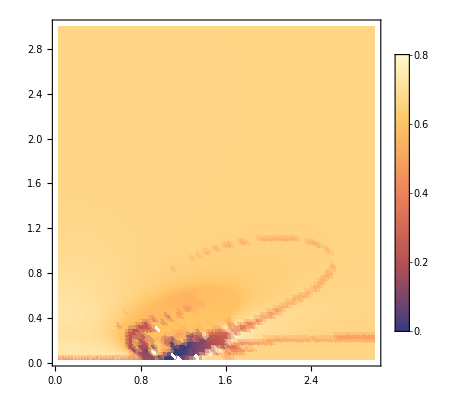

```mathematica
ListDensityPlot[Flatten[data,1],PlotRange->{All,All,{0,0.8}},PlotLegends->Automatic]
```

```mathematica
matrix={D[{dtlam1fun[h,Ttilde,mutilde,lam1bar,lam2bar,lam3bar],dtlam2fun[h,Ttilde,mutilde,lam1bar,lam2bar,lam3bar],dtlam3fun[h,Ttilde,mutilde,lam1bar,lam2bar,lam3bar]},lam1bar],D[{dtlam1fun[h,Ttilde,mutilde,lam1bar,lam2bar,lam3bar],dtlam2fun[h,Ttilde,mutilde,lam1bar,lam2bar,lam3bar],dtlam3fun[h,Ttilde,mutilde,lam1bar,lam2bar,lam3bar]},lam2bar],D[{dtlam1fun[h,Ttilde,mutilde,lam1bar,lam2bar,lam3bar],dtlam2fun[h,Ttilde,mutilde,lam1bar,lam2bar,lam3bar],dtlam3fun[h,Ttilde,mutilde,lam1bar,lam2bar,lam3bar]},lam3bar]};
```

```mathematica
-Select[Eigenvalues[matrix/.{Ttilde->2,mutilde->0,h->13/2}/.fixedPoints[2,0]]^-1,#<0&][[1]]
```

0.666696239325964755

## O(4) model high temperature limit

```mathematica
Series[1/2+1/(Exp[(√(1+mpibar2[rho]))/Ttilde]-1),{Ttilde,∞,2}]
```

Ttilde/(√(1+mpibar2[rho]))+(√(1+mpibar2[rho]))/(12 Ttilde)+O[1/Ttilde]^3

```mathematica
dtVbar[rho_]:=-3Vbar[rho]+rho lam1bar[rho]+1/(6 π^2)(3/(1+mpibar2[rho])+1/(1+msigmabar2[rho]));
dtlam1[rho_]:=D[dtVbar[rho],rho]
dtlam2[rho_]:=D[dtlam1[rho],rho]
dtlam3[rho_]:=D[dtlam2[rho],rho]
dtlam4[rho_]:=D[dtlam3[rho],rho]
dtlam5[rho_]:=D[dtlam4[rho],rho]
```

```mathematica
rep={mfbar2[rho]->mfbar2,mfbar2'[rho]->mfbar2d1rho,mpibar2[rho]->mpibar2,mpibar2'[rho]->mpibar2d1rho,msigmabar2[rho]->msigmabar2,msigmabar2'[rho]->msigmabar2d1rho,mfbar2''[rho]->mfbar2d2rho,mpibar2''[rho]->mpibar2d2rho,msigmabar2''[rho]->msigmabar2d2rho,Derivative[3][mfbar2][rho]->mfbar2d3rho,Derivative[3][mpibar2][rho]->mpibar2d3rho,Derivative[3][msigmabar2][rho]->msigmabar2d3rho};
```

```mathematica
mpibar2=lam1bar;
msigmabar2=lam1bar+2rhobar lam2bar;
mpibar2d1rho=D[lam1bar[rho],rho]/.{lam1bar'[rho]->lam2bar};
mpibar2d2rho=D[lam1bar[rho],{rho,2}]/.{lam1bar''[rho]->lam3bar};
mpibar2d3rho=D[lam1bar[rho],{rho,3}]/.{Derivative[3][lam1bar][rho]->lam4bar};
mpibar2d4rho=D[lam1bar[rho],{rho,4}]/.{Derivative[4][lam1bar][rho]->lam5bar};
mpibar2d5rho=D[lam1bar[rho],{rho,5}]/.{Derivative[5][lam1bar][rho]->0};
msigmabar2d1rho=D[lam1bar[rho]+2rho lam2bar[rho],rho]/.{lam1bar'[rho]->lam2bar,lam2bar[rho]->lam2bar,lam2bar'[rho]->lam3bar};
msigmabar2d2rho=D[lam1bar[rho]+2rho lam2bar[rho],{rho,2}]/.{lam1bar''[rho]->lam3bar,lam2bar'[rho]->lam3bar,lam2bar''[rho]->lam4bar};
msigmabar2d3rho=D[lam1bar[rho]+2rho lam2bar[rho],{rho,3}]/.{lam2bar''[rho]->lam4bar,Derivative[3][lam2bar][rho]->lam5bar,Derivative[3][lam1bar][rho]->lam4bar};
msigmabar2d4rho=D[lam1bar[rho]+2rho lam2bar[rho],{rho,4}]/.{Derivative[4][lam1bar][rho]->lam5bar,Derivative[4][lam2bar][rho]->0,Derivative[3][lam2bar][rho]->lam5bar};
msigmabar2d5rho=D[lam1bar[rho]+2rho lam2bar[rho],{rho,5}]/.{Derivative[4][lam2bar][rho]->0,Derivative[5][lam1bar][rho]->0,Derivative[5][lam2bar][rho]->0};
```

```mathematica
dtlam1exp=dtlam1[rho]/.rep/.{rhobar->0,rho->0}/.{Vbar'[0]->lam1bar}
dtlam2exp=dtlam2[rho]/.rep//.{rhobar->0,rho->0,Vbar''[0]->lam2bar};
dtlam3exp=dtlam3[rho]/.rep//.{rhobar->0,rho->0,Derivative[3][Vbar][0]->lam3bar};
dtlam4exp=dtlam4[rho]/.rep//.{rhobar->0,rho->0,Derivative[3][Vbar][0]->lam3bar,Derivative[4][lam1bar][0]->lam5bar,Derivative[4][Vbar][0]->lam4bar};
dtlam5exp=dtlam5[rho]/.rep//.{rhobar->0,rho->0,Derivative[3][Vbar][0]->lam3bar,Derivative[4][lam1bar][0]->lam5bar,Derivative[5][lam1bar][0]->0,Derivative[5][Vbar][0]->0};
```

-2 lam1bar-lam2bar/((1+lam1bar)^2 π^2)

```mathematica
dtlam1fun[lam1bar_,lam2bar_,lam3bar_,lam4bar_,lam5bar_]:=dtlam1exp;
dtlam2fun[lam1bar_,lam2bar_,lam3bar_,lam4bar_,lam5bar_]:=dtlam2exp;
dtlam3fun[lam1bar_,lam2bar_,lam3bar_,lam4bar_,lam5bar_]:=dtlam3exp;
dtlam4fun[lam1bar_,lam2bar_,lam3bar_,lam4bar_,lam5bar_]:=dtlam4exp;
dtlam5fun[lam1bar_,lam2bar_,lam3bar_,lam4bar_,lam5bar_]:=dtlam5exp;
```

## Fix point 1

```mathematica
FindRoot[{dtlam1fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar]==0.,dtlam2fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar]==0.,dtlam3fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar]==0.,dtlam4fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar]==0.,dtlam5fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar]==0.},{{lam1bar,-0.5},{lam2bar,0.5},{lam3bar,0.3},{lam4bar,0.},{lam5bar,0.}}]
```

{lam1bar→-0.0321667,lam2bar→0.594754,lam3bar→-3.02735,lam4bar→-24.1349,lam5bar→-85.4318}

```mathematica
matrix={D[{dtlam1fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam2fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam3fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam4fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam5fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar]},lam1bar],D[{dtlam1fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam2fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam3fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam4fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam5fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar]},lam2bar],D[{dtlam1fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam2fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam3fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam4fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam5fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar]},lam3bar],D[{dtlam1fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam2fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam3fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam4fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam5fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar]},lam4bar],D[{dtlam1fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam2fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam3fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam4fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam5fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar]},lam5bar]};
```

```mathematica
Eigenvalues[matrix/.{lam1bar->-0.032166728475587596,lam2bar->0.5947544908962089,lam3bar->-3.027352754406619,lam4bar->-24.134858677760725,lam5bar->-85.4318421573408}]
```

{7.39216,3.32234,-2.01218,-1.22613,0.176828}

```mathematica
{7.3921630590342975,3.3223378811406876,-2.01218326742499,-1.2261317655187876,0.1768283247440506}^-1
```

{0.135278,0.300993,-0.496973,-0.815573,5.6552}

## Fix point 2

```mathematica
FindRoot[{dtlam1fun[lam1bar,lam2bar,lam3bar]==0.,dtlam2fun[lam1bar,lam2bar,lam3bar]==0.,dtlam3fun[lam1bar,lam2bar,lam3bar]==0.},{{lam1bar,-0.4},{lam2bar,0.5},{lam3bar,0.1}}]
```

{lam1bar→-4.25805×10^-11,lam2bar→8.40506×10^-10,lam3bar→-6.2216×10^-9}

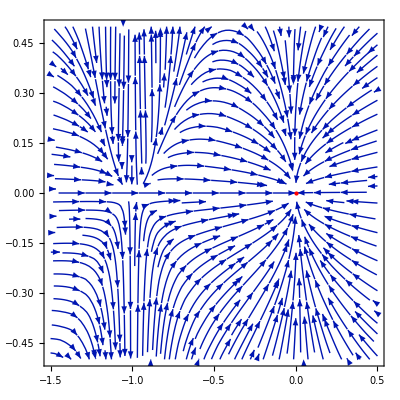

```mathematica
StreamPlot[{dtlam1fun[lam1bar,lam2bar,-6.22159695977147*^-9],dtlam2fun[lam1bar,lam2bar,-6.22159695977147*^-9]},{lam1bar,-1.5,0.5},{lam2bar,-0.5,0.5},StreamPoints->{500,0.01},Epilog->{Red,PointSize[Large],Point[{-4.258053598987462*^-11,8.405060908128205*^-10}]}]
```

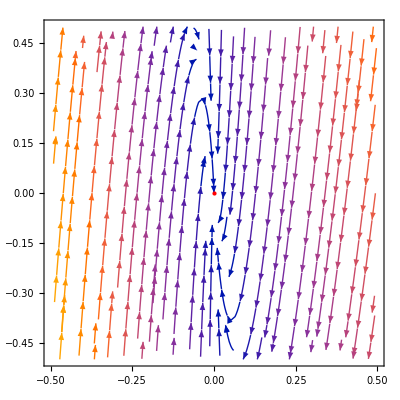

```mathematica
StreamPlot[{dtlam1fun[-4.258053598987462*^-11,lam2bar,lam3bar],dtlam2fun[-4.258053598987462*^-11,lam2bar,lam3bar]},{lam2bar,-0.5,0.5},{lam3bar,-0.5,0.5},StreamPoints->{500,Automatic},Epilog->{Red,PointSize[Large],Point[{-4.258053598987462*^-11,8.405060908128205*^-10}]}]
```

```mathematica
matrix={D[{dtlam1fun[lam1bar,lam2bar,lam3bar],dtlam2fun[lam1bar,lam2bar,lam3bar],dtlam3fun[lam1bar,lam2bar,lam3bar]},lam1bar],D[{dtlam1fun[lam1bar,lam2bar,lam3bar],dtlam2fun[lam1bar,lam2bar,lam3bar],dtlam3fun[lam1bar,lam2bar,lam3bar]},lam2bar],D[{dtlam1fun[lam1bar,lam2bar,lam3bar],dtlam2fun[lam1bar,lam2bar,lam3bar],dtlam3fun[lam1bar,lam2bar,lam3bar]},lam3bar]};
```

```mathematica
Eigenvalues[matrix/.{lam1bar->-4.258053598987462*^-11,lam2bar->8.405060908128205*^-10,lam3bar->-6.22159695977147*^-9}]
```

{-2.,-1.,3.0658×10^-9}

```mathematica
{-2.000000000000001,-1.0000000006812892,3.06579858933458*^-9}^-1
```

{-0.5,-1.,3.26179×10^8}

## Fix point 3

```mathematica
FindRoot[{dtlam1fun[lam1bar,lam2bar,lam3bar]==0.,dtlam2fun[lam1bar,lam2bar,lam3bar]==0.,dtlam3fun[lam1bar,lam2bar,lam3bar]==0.},{{lam1bar,-0.7},{lam2bar,1.9},{lam3bar,0.3}}]
```

{lam1bar→-3.80977×10^-11,lam2bar→7.52018×10^-10,lam3bar→-5.56659×10^-9}

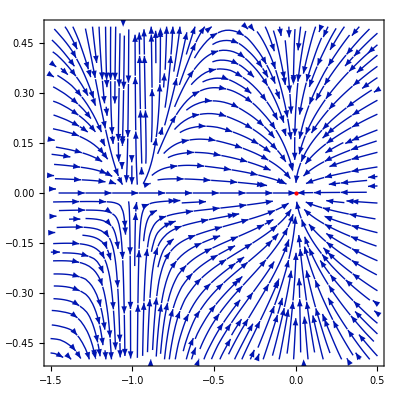

```mathematica
StreamPlot[{dtlam1fun[lam1bar,lam2bar,-6.22159695977147*^-9],dtlam2fun[lam1bar,lam2bar,-6.22159695977147*^-9]},{lam1bar,-1.5,0.5},{lam2bar,-0.5,0.5},StreamPoints->{500,0.01},Epilog->{Red,PointSize[Large],Point[{-4.258053598987462*^-11,8.405060908128205*^-10}]}]
```

```mathematica
matrix={D[{dtlam1fun[lam1bar,lam2bar,lam3bar],dtlam2fun[lam1bar,lam2bar,lam3bar],dtlam3fun[lam1bar,lam2bar,lam3bar]},lam1bar],D[{dtlam1fun[lam1bar,lam2bar,lam3bar],dtlam2fun[lam1bar,lam2bar,lam3bar],dtlam3fun[lam1bar,lam2bar,lam3bar]},lam2bar],D[{dtlam1fun[lam1bar,lam2bar,lam3bar],dtlam2fun[lam1bar,lam2bar,lam3bar],dtlam3fun[lam1bar,lam2bar,lam3bar]},lam3bar]};
```

```mathematica
Eigenvalues[matrix/.{lam1bar->-4.258053598987462*^-11,lam2bar->8.405060908128205*^-10,lam3bar->-6.22159695977147*^-9}]
```

{-2.,-1.,3.0658×10^-9}

```mathematica
{-2.000000000000001,-1.0000000006812892,3.06579858933458*^-9}^-1
```

{-0.5,-1.,3.26179×10^8}

## O(4) model high temperature limit Nv=2

```mathematica
Series[1/2+1/(Exp[(√(1+mpibar2[rho]))/Ttilde]-1),{Ttilde,∞,2}]
```

Ttilde/(√(1+mpibar2[rho]))+(√(1+mpibar2[rho]))/(12 Ttilde)+O[1/Ttilde]^3

```mathematica
dtVbar[rho_]:=-3Vbar[rho]+rho lam1bar[rho]+1/(6 π^2)(3/(1+mpibar2[rho])+1/(1+msigmabar2[rho]));
dtlam1[rho_]:=D[dtVbar[rho],rho]
dtlam2[rho_]:=D[dtlam1[rho],rho]
```

```mathematica
rep={mfbar2[rho]->mfbar2,mfbar2'[rho]->mfbar2d1rho,mpibar2[rho]->mpibar2,mpibar2'[rho]->mpibar2d1rho,msigmabar2[rho]->msigmabar2,msigmabar2'[rho]->msigmabar2d1rho,mfbar2''[rho]->mfbar2d2rho,mpibar2''[rho]->mpibar2d2rho,msigmabar2''[rho]->msigmabar2d2rho,Derivative[3][mfbar2][rho]->mfbar2d3rho,Derivative[3][mpibar2][rho]->mpibar2d3rho,Derivative[3][msigmabar2][rho]->msigmabar2d3rho};
```

```mathematica
mpibar2=lam1bar;
msigmabar2=lam1bar+2rhobar lam2bar;
mpibar2d1rho=D[lam1bar[rho],rho]/.{lam1bar'[rho]->lam2bar};
mpibar2d2rho=D[lam1bar[rho],{rho,2}]/.{lam1bar''[rho]->0};
msigmabar2d1rho=D[lam1bar[rho]+2rho lam2bar[rho],rho]/.{lam1bar'[rho]->lam2bar,lam2bar[rho]->lam2bar,lam2bar'[rho]->0};
msigmabar2d2rho=D[lam1bar[rho]+2rho lam2bar[rho],{rho,2}]/.{lam1bar''[rho]->0,lam2bar'[rho]->0,lam2bar''[rho]->0};
```

```mathematica
dtlam1exp=dtlam1[rho]/.rep/.{rhobar->0,rho->0}/.{Vbar'[0]->lam1bar}
dtlam2exp=dtlam2[rho]/.rep//.{rhobar->0,rho->0,Vbar''[0]->lam2bar}/.{lam3bar->0}
```

-2 lam1bar-lam2bar/((1+lam1bar)^2 π^2)

-lam2bar+(4 lam2bar^2)/((1+lam1bar)^3 π^2)

```mathematica
dtlam1fun[lam1bar_,lam2bar_]:=dtlam1exp;
dtlam2fun[lam1bar_,lam2bar_]:=dtlam2exp;
```

## Fix point 1

```mathematica
Solve[{dtlam1fun[lam1bar,lam2bar]==0,dtlam2fun[lam1bar,lam2bar]==0},{lam1bar,lam2bar}]
```

{{lam1bar→-1/9,lam2bar→(128 π^2)/729},{lam1bar→0,lam2bar→0}}

```mathematica
matrix={D[{dtlam1fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam2fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam3fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam4fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam5fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar]},lam1bar],D[{dtlam1fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam2fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam3fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam4fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam5fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar]},lam2bar],D[{dtlam1fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam2fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam3fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam4fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam5fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar]},lam3bar],D[{dtlam1fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam2fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam3fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam4fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam5fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar]},lam4bar],D[{dtlam1fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam2fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam3fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam4fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam5fun[lam1bar,lam2bar,lam3bar,lam4bar,lam5bar]},lam5bar]};
```

```mathematica
Eigenvalues[matrix/.{lam1bar->-0.032166728475587596,lam2bar->0.5947544908962089,lam3bar->-3.027352754406619,lam4bar->-24.134858677760725,lam5bar->-85.4318421573408}]
```

{7.39216,3.32234,-2.01218,-1.22613,0.176828}

```mathematica
{7.3921630590342975,3.3223378811406876,-2.01218326742499,-1.2261317655187876,0.1768283247440506}^-1
```

{0.135278,0.300993,-0.496973,-0.815573,5.6552}

## O(4) model high temperature limit Nv=3

```mathematica
Series[1/2+1/(Exp[(√(1+mpibar2[rho]))/Ttilde]-1),{Ttilde,∞,2}]
```

Ttilde/(√(1+mpibar2[rho]))+(√(1+mpibar2[rho]))/(12 Ttilde)+O[1/Ttilde]^3

```mathematica
dtVbar[rho_]:=-3Vbar[rho]+rho lam1bar[rho]+1/(6 π^2)((N1-1)/(1+lam1bar[rho])+1/(1+(lam1bar[rho]+2rho lam2bar[rho])));
dtlam1[rho_]:=D[dtVbar[rho],rho]
dtlam2[rho_]:=D[dtlam1[rho],rho]
dtlam3[rho_]:=D[dtlam2[rho],rho]
```

```mathematica
rep={lam1bar[0]->lam1bar,lam1bar'[0]->lam2bar,lam1bar''[0]->lam3bar,Derivative[3][lam1bar][0]->0,lam2bar[0]->lam2bar,lam2bar'[0]->lam3bar,lam2bar''[0]->0,Vbar'[0]->lam1bar,Vbar''[0]->lam2bar,Derivative[3][Vbar][0]->lam3bar};
```

```mathematica
dtlam1exp=dtlam1[rho]/.{rho->0}/.rep
dtlam2exp=dtlam2[rho]/.{rho->0}/.rep
dtlam3exp=dtlam3[rho]/.{rho->0}/.rep
```

-2 lam1bar+(-(3 lam2bar)/(1+lam1bar)^2-(lam2bar (-1+N1))/(1+lam1bar)^2)/(6 π^2)

-lam2bar+((18 lam2bar^2)/(1+lam1bar)^3-(5 lam3bar)/(1+lam1bar)^2+(2 lam2bar^2 (-1+N1))/(1+lam1bar)^3-(lam3bar (-1+N1))/(1+lam1bar)^2)/(6 π^2)

(-(162 lam2bar^3)/(1+lam1bar)^4+(90 lam2bar lam3bar)/(1+lam1bar)^3-(6 lam2bar^3 (-1+N1))/(1+lam1bar)^4+(6 lam2bar lam3bar (-1+N1))/(1+lam1bar)^3)/(6 π^2)

```mathematica
dtlam1fun[N1_,lam1bar_,lam2bar_,lam3bar_]:=-2 lam1bar+(-(3 lam2bar)/(1+lam1bar)^2-(lam2bar (-1+N1))/(1+lam1bar)^2)/(6 π^2);
dtlam2fun[N1_,lam1bar_,lam2bar_,lam3bar_]:=-lam2bar+((18 lam2bar^2)/(1+lam1bar)^3-(5 lam3bar)/(1+lam1bar)^2+(2 lam2bar^2 (-1+N1))/(1+lam1bar)^3-(lam3bar (-1+N1))/(1+lam1bar)^2)/(6 π^2);
dtlam3fun[N1_,lam1bar_,lam2bar_,lam3bar_]:=(-(162 lam2bar^3)/(1+lam1bar)^4+(90 lam2bar lam3bar)/(1+lam1bar)^3-(6 lam2bar^3 (-1+N1))/(1+lam1bar)^4+(6 lam2bar lam3bar (-1+N1))/(1+lam1bar)^3)/(6 π^2);
```

## Fix point 1

```mathematica
FindRoot[{dtlam1fun[n,lam1bar,lam2bar,lam3bar]==0,dtlam2fun[n,lam1bar,lam2bar,lam3bar]==0,dtlam3fun[n,lam1bar,lam2bar,lam3bar]==0},{{lam1bar,-1/9},{lam2bar,(128 π^2)/729},{lam3bar,0.}}]
```

{lam1bar→7.00219×10^-11,lam2bar→-1.38218×10^-9,lam3bar→1.02312×10^-8}

```mathematica
matrix={D[{dtlam1fun[n,lam1bar,lam2bar,lam3bar],dtlam2fun[n,lam1bar,lam2bar,lam3bar],dtlam3fun[n,lam1bar,lam2bar,lam3bar]},lam1bar],D[{dtlam1fun[n,lam1bar,lam2bar,lam3bar],dtlam2fun[n,lam1bar,lam2bar,lam3bar],dtlam3fun[n,lam1bar,lam2bar,lam3bar]},lam2bar],D[{dtlam1fun[n,lam1bar,lam2bar,lam3bar],dtlam2fun[n,lam1bar,lam2bar,lam3bar],dtlam3fun[n,lam1bar,lam2bar,lam3bar]},lam3bar]};
```

```mathematica
Eigenvalues[matrix/.{lam1bar->0,lam2bar->0,lam3bar->0}]
```

{-2,-1,0}

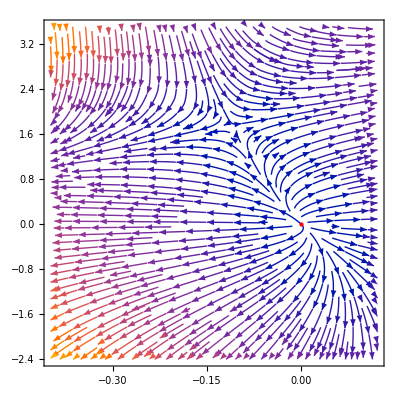

```mathematica
myStreamPlot[{-dtlam1fun[n,lam1bar,lam2bar,0.],-dtlam2fun[n,lam1bar,lam2bar,0.]},{lam1bar,-0.4(*-13/41*),5/41},{lam2bar,-2.4,3.5},StreamPoints->{500,0.005},Epilog->{Red,PointSize[Large],Point[{0,0}]}]
```

## Fix point 2

```mathematica
n=4;
Solve[{-dtlam1fun[n,lam1bar,lam2bar,lam3bar]==0,-dtlam2fun[n,lam1bar,lam2bar,lam3bar]==0,-dtlam3fun[n,lam1bar,lam2bar,lam3bar]==0},{lam1bar,lam2bar,lam3bar}]
```

{{lam1bar→-9/41,lam2bar→(18432 π^2)/68921,lam3bar→(17694720 π^4)/115856201},{lam1bar→0,lam2bar→0,lam3bar→0}}

```mathematica
matrix={D[{dtlam1fun[n,lam1bar,lam2bar,lam3bar],dtlam2fun[n,lam1bar,lam2bar,lam3bar],dtlam3fun[n,lam1bar,lam2bar,lam3bar]},lam1bar],D[{dtlam1fun[n,lam1bar,lam2bar,lam3bar],dtlam2fun[n,lam1bar,lam2bar,lam3bar],dtlam3fun[n,lam1bar,lam2bar,lam3bar]},lam2bar],D[{dtlam1fun[n,lam1bar,lam2bar,lam3bar],dtlam2fun[n,lam1bar,lam2bar,lam3bar],dtlam3fun[n,lam1bar,lam2bar,lam3bar]},lam3bar]};
```

```mathematica
eign=Eigenvalues[matrix/.{lam1bar->-9/41,lam2bar->(18432 π^2)/68921,lam3bar->(17694720 π^4)/115856201}]//N
```

{12.9187,-1.50401,1.33533}

```mathematica
eign^-1//N
```

{0.0774073,-0.664888,0.748878}

```mathematica
Options[myStreamPlot]=Options[StreamPlot];
myStreamPlot[f_,{x_,x0_,x1_},{y_,y0_,y1_},opts:OptionsPattern[]]:=With[{a=OptionValue[AspectRatio]},Show[StreamPlot[{1/(x1-x0),a/(y1-y0)} (f/. {x->x0+u (x1-x0),y->y0+v/a (y1-y0)}),{u,0,1},{v,0,a},opts]/. Arrow[pts_]:>Arrow[({x0,y0}+{x1-x0,(y1-y0)/a} #)&/@pts],PlotRange->{{x0,x1},{y0,y1}}]]
```

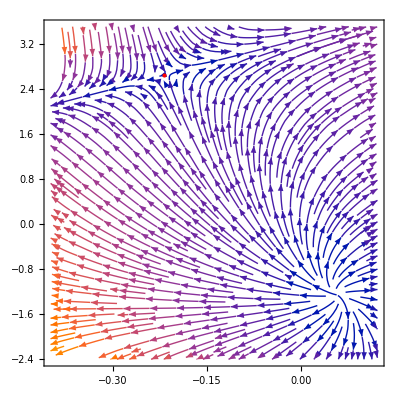

```mathematica
myStreamPlot[{-dtlam1fun[n,lam1bar,lam2bar,N[(17694720 π^4)/115856201]],-dtlam2fun[n,lam1bar,lam2bar,N[(17694720 π^4)/115856201]]},{lam1bar,-0.4(*-13/41*),5/41},{lam2bar,-2.4,3.5},StreamPoints->{200,0.004},Epilog->{Red,PointSize[Large],Point[{-9/41,(18432 π^2)/68921}]}]
```

## O(4) model high temperature limit Nv=3 d=4

```mathematica
Series[1/2+1/(Exp[(√(1+mpibar2[rho]))/Ttilde]-1),{Ttilde,∞,2}]
```

Ttilde/(√(1+mpibar2[rho]))+(√(1+mpibar2[rho]))/(12 Ttilde)+O[1/Ttilde]^3

```mathematica
dtVbar[rho_]:=-3Vbar[rho]+rho lam1bar[rho]+1/(6 π^2)(3/(1+mpibar2[rho])+1/(1+msigmabar2[rho]));
dtlam1[rho_]:=D[dtVbar[rho],rho]
dtlam2[rho_]:=D[dtlam1[rho],rho]
dtlam3[rho_]:=D[dtlam2[rho],rho]
```

```mathematica
rep={lam1bar[0]->lam1bar,lam1bar'[0]->lam2bar,lam1bar''[0]->lam3bar,Derivative[3][lam1bar][0]->0};
```

```mathematica
mpibar2=lam1bar;
msigmabar2=lam1bar+2rhobar lam2bar;
mpibar2d1rho=D[lam1bar[rho],rho]/.{lam1bar'[rho]->lam2bar};
mpibar2d2rho=D[lam1bar[rho],{rho,2}]/.{lam1bar''[rho]->lam3bar};
mpibar2d3rho=D[lam1bar[rho],{rho,3}]/.{Derivative[3][lam1bar][rho]->0};
msigmabar2d1rho=D[lam1bar[rho]+2rho lam2bar[rho],rho]/.{lam1bar'[rho]->lam2bar,lam2bar[rho]->lam2bar,lam2bar'[rho]->lam3bar};
msigmabar2d2rho=D[lam1bar[rho]+2rho lam2bar[rho],{rho,2}]/.{lam1bar''[rho]->lam3bar,lam2bar'[rho]->lam3bar,lam2bar''[rho]->0};
msigmabar2d3rho=D[lam1bar[rho]+2rho lam2bar[rho],{rho,3}]/.{lam2bar''[rho]->0,Derivative[3][lam2bar][rho]->0,Derivative[3][lam1bar][rho]->0};
```

```mathematica
dtlam1exp=dtlam1[rho]/.{rhobar->0,rho->0}/.{Vbar'[0]->lam1bar}/.rep
dtlam2exp=dtlam2[rho]//.{rhobar->0,rho->0,Vbar''[0]->lam2bar}/.rep
dtlam3exp=dtlam3[rho]//.{rhobar->0,rho->0,Derivative[3][Vbar][0]->lam3bar,lam4bar->0}/.rep
```

-2 lam1bar-lam2bar/(8 (1+lam1bar)^2 π^2)

((8 lam2bar^2)/(1+lam1bar)^3-(4 lam3bar)/(1+lam1bar)^2)/(32 π^2)

2 lam3bar+(-(24 lam2bar^3)/(1+lam1bar)^4+(24 lam2bar lam3bar)/(1+lam1bar)^3)/(32 π^2)

```mathematica
dtlam1fun[lam1bar_,lam2bar_,lam3bar_]:=-2 lam1bar-lam2bar/(8 (1+lam1bar)^2 π^2);
dtlam2fun[lam1bar_,lam2bar_,lam3bar_]:=((8 lam2bar^2)/(1+lam1bar)^3-(4 lam3bar)/(1+lam1bar)^2)/(32 π^2);
dtlam3fun[lam1bar_,lam2bar_,lam3bar_]:=2 lam3bar+(-(24 lam2bar^3)/(1+lam1bar)^4+(24 lam2bar lam3bar)/(1+lam1bar)^3)/(32 π^2);
```

## Fix point 1

```mathematica
FindRoot[{dtlam1fun[lam1bar,lam2bar,lam3bar]==0,dtlam2fun[lam1bar,lam2bar,lam3bar]==0,dtlam3fun[lam1bar,lam2bar,lam3bar]==0},{{lam1bar,-1/9},{lam2bar,(128 π^2)/729},{lam3bar,0.}}]
```

{lam1bar→-5.42688×10^-11,lam2bar→8.56979×10^-9,lam3bar→-9.56537×10^-26}

```mathematica
matrix={D[{dtlam1fun[lam1bar,lam2bar,lam3bar],dtlam2fun[lam1bar,lam2bar,lam3bar],dtlam3fun[lam1bar,lam2bar,lam3bar]},lam1bar],D[{dtlam1fun[lam1bar,lam2bar,lam3bar],dtlam2fun[lam1bar,lam2bar,lam3bar],dtlam3fun[lam1bar,lam2bar,lam3bar]},lam2bar],D[{dtlam1fun[lam1bar,lam2bar,lam3bar],dtlam2fun[lam1bar,lam2bar,lam3bar],dtlam3fun[lam1bar,lam2bar,lam3bar]},lam3bar]};
```

```mathematica
eigen=Eigenvalues[matrix/.{lam1bar->0,lam2bar->0,lam3bar->0}]
```

{-2,2,0}

```mathematica
eigen^-1
```

Power::infy: 碰到无穷表达式 1/0.

{-1/2,1/2,ComplexInfinity}

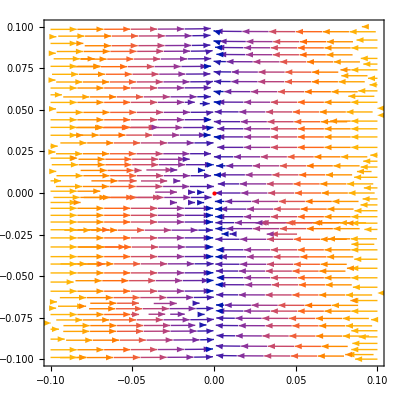

```mathematica
StreamPlot[{dtlam1fun[lam1bar,lam2bar,0.],dtlam2fun[lam1bar,lam2bar,0.]},{lam1bar,-0.1,0.1},{lam2bar,-0.1,0.1},StreamPoints->{500,0.001},Epilog->{Red,PointSize[Large],Point[{0,0}]}]
```

## Fix point 2

```mathematica
Solve[{dtlam1fun[lam1bar,lam2bar,lam3bar]==0,dtlam2fun[lam1bar,lam2bar,lam3bar]==0,dtlam3fun[lam1bar,lam2bar,lam3bar]==0},{lam1bar,lam2bar,lam3bar}]
```

{{lam1bar→0,lam2bar→0,lam3bar→0},{lam1bar→1/2,lam2bar→-18 π^2,lam3bar→432 π^4}}

```mathematica
matrix={D[{dtlam1fun[lam1bar,lam2bar,lam3bar],dtlam2fun[lam1bar,lam2bar,lam3bar],dtlam3fun[lam1bar,lam2bar,lam3bar]},lam1bar],D[{dtlam1fun[lam1bar,lam2bar,lam3bar],dtlam2fun[lam1bar,lam2bar,lam3bar],dtlam3fun[lam1bar,lam2bar,lam3bar]},lam2bar],D[{dtlam1fun[lam1bar,lam2bar,lam3bar],dtlam2fun[lam1bar,lam2bar,lam3bar],dtlam3fun[lam1bar,lam2bar,lam3bar]},lam3bar]};
```

```mathematica
eign=Eigenvalues[matrix/.{lam1bar->1/2,lam2bar->-18 π^2,lam3bar->432 π^4}]//N
```

{-3.88573+0.676993 ⅈ,-3.88573-0.676993 ⅈ,-0.228547}

```mathematica
eign^-1//N
```

{-0.257352,-0.257352,-4.37546}

## O(4) model high temperature limit Nv=5

```mathematica
Series[1/2+1/(Exp[(√(1+mpibar2[rho]))/Ttilde]-1),{Ttilde,∞,2}]
```

Ttilde/(√(1+mpibar2[rho]))+(√(1+mpibar2[rho]))/(12 Ttilde)+O[1/Ttilde]^3

```mathematica
dtVbar[rho_]:=-3Vbar[rho]+rho lam1bar[rho]+1/(6 π^2)((N1-1)/(1+lam1bar[rho])+1/(1+(lam1bar[rho]+2rho lam2bar[rho])));
dtlam1[rho_]:=D[dtVbar[rho],rho]
dtlam2[rho_]:=D[dtlam1[rho],rho]
dtlam3[rho_]:=D[dtlam2[rho],rho]
dtlam4[rho_]:=D[dtlam3[rho],rho]
dtlam5[rho_]:=D[dtlam4[rho],rho]
```

```mathematica
rep={lam1bar[0]->lam1bar,lam1bar'[0]->lam2bar,lam1bar''[0]->lam3bar,Derivative[3][lam1bar][0]->0,lam2bar[0]->lam2bar,lam2bar'[0]->lam3bar,lam2bar''[0]->0,Vbar'[0]->lam1bar,Vbar''[0]->lam2bar,Derivative[3][Vbar][0]->lam3bar,Derivative[4][lam1bar][0]->lam4bar,Derivative[3][lam2bar][0]->lam5bar,Derivative[4][Vbar][0]->lam4bar,Derivative[4][lam2bar][0]->0,Derivative[5][lam1bar][0]->0,Derivative[5][Vbar][0]->lam5bar};
```

```mathematica
dtlam1exp=dtlam1[rho]/.{rho->0}/.rep
dtlam2exp=dtlam2[rho]/.{rho->0}/.rep
dtlam3exp=dtlam3[rho]/.{rho->0}/.rep
dtlam4exp=dtlam4[rho]/.{rho->0}/.rep
dtlam5exp=dtlam5[rho]/.{rho->0}/.rep
```

-2 lam1bar+(-(3 lam2bar)/(1+lam1bar)^2-(lam2bar (-1+N1))/(1+lam1bar)^2)/(6 π^2)

-lam2bar+((18 lam2bar^2)/(1+lam1bar)^3-(5 lam3bar)/(1+lam1bar)^2+(2 lam2bar^2 (-1+N1))/(1+lam1bar)^3-(lam3bar (-1+N1))/(1+lam1bar)^2)/(6 π^2)

(-(162 lam2bar^3)/(1+lam1bar)^4+(90 lam2bar lam3bar)/(1+lam1bar)^3-(6 lam2bar^3 (-1+N1))/(1+lam1bar)^4+(6 lam2bar lam3bar (-1+N1))/(1+lam1bar)^3)/(6 π^2)

-3 lam4bar+((1944 lam2bar^4)/(1+lam1bar)^5-(1620 lam2bar^2 lam3bar)/(1+lam1bar)^4+(150 lam3bar^2)/(1+lam1bar)^3-(lam4bar+8 lam5bar)/(1+lam1bar)^2+(24 lam2bar^4 (-1+N1))/(1+lam1bar)^5-(36 lam2bar^2 lam3bar (-1+N1))/(1+lam1bar)^4+(6 lam3bar^2 (-1+N1))/(1+lam1bar)^3-(lam4bar (-1+N1))/(1+lam1bar)^2)/(6 π^2)

5 lam4bar-3 lam5bar+1/(6 π^2)(-(29160 lam2bar^5)/(1+lam1bar)^6+(32400 lam2bar^3 lam3bar)/(1+lam1bar)^5-(6750 lam2bar lam3bar^2)/(1+lam1bar)^4+(30 lam2bar (lam4bar+8 lam5bar))/(1+lam1bar)^3-(120 lam2bar^5 (-1+N1))/(1+lam1bar)^6+(240 lam2bar^3 lam3bar (-1+N1))/(1+lam1bar)^5-(90 lam2bar lam3bar^2 (-1+N1))/(1+lam1bar)^4+(10 lam2bar lam4bar (-1+N1))/(1+lam1bar)^3)

```mathematica
dtlam1fun[N1_,lam1bar_,lam2bar_,lam3bar_,lam4bar_,lam5bar_]=dtlam1exp;
dtlam2fun[N1_,lam1bar_,lam2bar_,lam3bar_,lam4bar_,lam5bar_]=dtlam2exp;
dtlam3fun[N1_,lam1bar_,lam2bar_,lam3bar_,lam4bar_,lam5bar_]=dtlam3exp;
dtlam4fun[N1_,lam1bar_,lam2bar_,lam3bar_,lam4bar_,lam5bar_]=dtlam4exp;
dtlam5fun[N1_,lam1bar_,lam2bar_,lam3bar_,lam4bar_,lam5bar_]=dtlam5exp;
```

## Fix point 2

```mathematica
n=4;
Solve[{dtlam1fun[4,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar]==0,dtlam2fun[4,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar]==0,dtlam3fun[4,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar]==0,dtlam4fun[4,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar]==0,dtlam5fun[4,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar]==0},{lam1bar,lam2bar,lam3bar,lam4bar,lam5bar}]
```

{{lam1bar→-9/41,lam2bar→(18432 π^2)/68921,lam3bar→(17694720 π^4)/115856201,lam4bar→(10965262496956416 π^8)/(2291673540757727-69999360135404544 π^2),lam5bar→(-11274897017379225600 π^8+37615957859138273280 π^10)/(3852303222013739087-117668924387615038464 π^2)},{lam1bar→0,lam2bar→0,lam3bar→0,lam4bar→0,lam5bar→0}}

```mathematica
matrix={D[{dtlam1fun[n,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam2fun[n,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam3fun[n,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam4fun[n,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam5fun[n,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar]},lam1bar],D[{dtlam1fun[n,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam2fun[n,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam3fun[n,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam4fun[n,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam5fun[n,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar]},lam2bar],D[{dtlam1fun[n,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam2fun[n,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam3fun[n,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam4fun[n,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam5fun[n,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar]},lam3bar],D[{dtlam1fun[n,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam2fun[n,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam3fun[n,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam4fun[n,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam5fun[n,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar]},lam4bar],D[{dtlam1fun[n,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam2fun[n,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam3fun[n,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam4fun[n,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar],dtlam5fun[n,lam1bar,lam2bar,lam3bar,lam4bar,lam5bar]},lam5bar]};
```

```mathematica
eign=Eigenvalues[matrix/.{lam1bar->-9/41,lam2bar->(18432 π^2)/68921,lam3bar->(17694720 π^4)/115856201,lam4bar->(10965262496956416 π^8)/(2291673540757727-69999360135404544 π^2),lam5bar->(-11274897017379225600 π^8+37615957859138273280 π^10)/(3852303222013739087-117668924387615038464 π^2)}]//N
```

{19.3953,12.9187,-3.00619,-1.50401,1.33533}

```mathematica
eign^-1//N
```

{0.0515589,0.0774073,-0.332647,-0.664888,0.748878}